# Reversible CAs (version 20-10-2022)

## Standard reversible rules

### k = 2, r = 1

```mathematica
Select[Range[0,2^(2^3)-1],ReversibleRuleQ[#,2,1]&]
```

{15,51,85,170,204,240}

```mathematica
GatherBy[{15,51,85,170,204,240},Sort@DynamicalEquivalenceClass[#]&]//MatrixForm
```

({15,85}
{51}
{170,240}
{204})

```mathematica
{#, InverseRule[#]}&/@%%//MatrixForm
```

(15 | {85,2,1}
51 | {51,2,1}
85 | {15,2,1}
170 | {240,2,1}
204 | {204,2,1}
240 | {170,2,1})

```mathematica
InverseRule[15]
```

{85,2,1}

```mathematica
First/@GatherBy[{#,2,1}&/@{15,51,85,170,204,240},Sort@DynamicalEquivalenceClass[Sequence@@#]&]
```

{{15,2,1},{51,2,1},{170,2,1},{204,2,1}}

```mathematica
{#,RuleMinDNF[#,1]}&/@(First/@%)//MatrixForm
```

(15 | (!x)_-1
51 | (!x)_0
170 | x_1
204 | x_0)

### k = 2, r = 1.5

```mathematica
Select[Range[0,2^(2^4)-1],ReversibleRuleQ[#,2,1.5]&]
```

{255,3855,3915,11535,13107,13155,14643,21845,43690,50892,52380,52428,54000,61620,61680,65280}

```mathematica
GatherBy[{#,2,1.5}&/@%,Sort@DynamicalEquivalenceClass[Sequence@@#]&]//MatrixForm
```

({{255,2,1.5},{21845,2,1.5}}
{{3855,2,1.5},{13107,2,1.5}}
{{3915,2,1.5}}
{{11535,2,1.5}}
{{13155,2,1.5}}
{{14643,2,1.5}}
{{43690,2,1.5},{65280,2,1.5}}
{{50892,2,1.5}}
{{52380,2,1.5}}
{{52428,2,1.5},{61680,2,1.5}}
{{54000,2,1.5}}
{{61620,2,1.5}})

```mathematica
First/@GatherBy[{#,2,1.5}&/@{255,3855,3915,11535,13107,13155,14643,21845,43690,50892,52380,52428,54000,61620,61680,65280},Sort@DynamicalEquivalenceClass[Sequence@@#]&]
```

{{255,2,1.5},{3855,2,1.5},{3915,2,1.5},{11535,2,1.5},{13155,2,1.5},{14643,2,1.5},{43690,2,1.5},{50892,2,1.5},{52380,2,1.5},{52428,2,1.5},{54000,2,1.5},{61620,2,1.5}}

```mathematica
GraphicsGrid[Module[{ic=RandomInteger[{0,1},100]},Partition[ArrayPlot[CellularAutomaton[{First@#,2,FlexRadius[1.5]},ic,150],PlotLabel->#]&/@%,4]]]
```

-Graphics-

```mathematica
{#,RuleMinDNF[#,1.5]}&/@(First/@{{255,2,1.5},{3855,2,1.5},{3915,2,1.5},{11535,2,1.5},{13155,2,1.5},{14643,2,1.5},{43690,2,1.5},{50892,2,1.5},{52380,2,1.5},{52428,2,1.5},{54000,2,1.5},{61620,2,1.5}})//MatrixForm
```

(255 | (!x)_-2
3855 | (!x)_-1
3915 | (x_-2&&(!x)_-1)||((!x)_-2&&x_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0)||((!x)_-1&&x_1)
11535 | (x_-2&&x_-1&&(!x)_0&&x_1)||((!x)_-2&&(!x)_-1)||((!x)_-1&&x_0)||((!x)_-1&&(!x)_1)
13155 | (x_-2&&(!x)_0)||((!x)_-2&&x_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0)||((!x)_0&&x_1)
14643 | (x_-2&&(!x)_-1&&x_0&&x_1)||((!x)_-2&&(!x)_0)||(x_-1&&(!x)_0)||((!x)_0&&(!x)_1)
43690 | x_1
50892 | (x_-2&&(!x)_-1&&(!x)_0&&x_1)||((!x)_-2&&x_0)||(x_-1&&x_0)||(x_0&&(!x)_1)
52380 | (x_-2&&x_0)||((!x)_-2&&x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0)||(x_0&&x_1)
52428 | x_0
54000 | (x_-2&&(!x)_-1&&(!x)_0&&x_1)||((!x)_-2&&x_-1)||(x_-1&&x_0)||(x_-1&&(!x)_1)
61620 | (x_-2&&x_-1)||((!x)_-2&&(!x)_-1&&x_0&&(!x)_1)||(x_-1&&(!x)_0)||(x_-1&&x_1))

```mathematica
{#, InverseRule[Sequence@@#]}&/@{{255,2,1.5},{3855,2,1.5},{3915,2,1.5},{11535,2,1.5},{13155,2,1.5},{14643,2,1.5},{43690,2,1.5},{50892,2,1.5},{52380,2,1.5},{52428,2,1.5},{54000,2,1.5},{61620,2,1.5}}//MatrixForm
```

$Aborted

### k = 3, r = 0.5

```mathematica
Select[Range[0,3^(3^2)-1],ReversibleRuleQ[#,3,0.5]&]
```

{377,481,611,715,1079,2119,2899,3785,3791,3841,4217,4745,5243,5299,5311,5515,7995,8321,8327,8439,8543,8801,9503,9711,9971,10179,10881,11139,11243,11355,11361,11687,14167,14371,14383,14439,14937,15465,15841,15891,15897,16783,17563,18603,18967,19071,19201,19305}

```mathematica
First/@GatherBy[{#,3,0.5}&/@%,Sort@DynamicalEquivalenceClass[Sequence@@#]&]
```

{{377,3,0.5},{481,3,0.5},{611,3,0.5},{715,3,0.5},{1079,3,0.5},{2119,3,0.5},{2899,3,0.5},{3791,3,0.5},{3841,3,0.5},{4217,3,0.5},{5243,3,0.5},{5311,3,0.5},{5515,3,0.5},{7995,3,0.5},{8321,3,0.5},{8439,3,0.5},{8543,3,0.5},{8801,3,0.5},{9711,3,0.5},{9971,3,0.5},{11139,3,0.5},{11243,3,0.5},{11687,3,0.5},{14167,3,0.5},{14371,3,0.5},{14439,3,0.5},{15897,3,0.5},{16783,3,0.5},{17563,3,0.5}}

```mathematica
GraphicsGrid[Module[{ic=RandomInteger[{0,1},100]},Partition[ArrayPlot[CellularAutomaton[{First@#,3,FlexRadius[0.5]},ic,150],PlotLabel->#]&/@%,6]]]
```

-Graphics-

```mathematica
{#, InverseRule[Sequence@@#]}&/@{{377,3,0.5},{481,3,0.5},{611,3,0.5},{715,3,0.5},{1079,3,0.5},{2119,3,0.5},{2899,3,0.5},{3791,3,0.5},{3841,3,0.5},{4217,3,0.5},{5243,3,0.5},{5311,3,0.5},{5515,3,0.5},{7995,3,0.5},{8321,3,0.5},{8439,3,0.5},{8543,3,0.5},{8801,3,0.5},{9711,3,0.5},{9971,3,0.5},{11139,3,0.5},{11243,3,0.5},{11687,3,0.5},{14167,3,0.5},{14371,3,0.5},{14439,3,0.5},{15897,3,0.5},{16783,3,0.5},{17563,3,0.5}}//MatrixForm
```

$Aborted

## Second-order, intrinsically reversible rules (a construction from the NKS book)

### The idea (with an ECA)

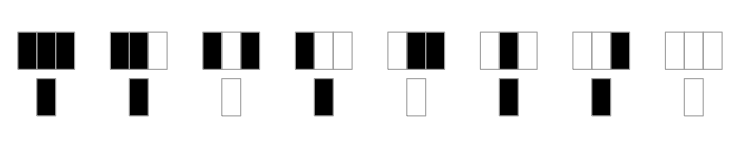

```mathematica
RulePlot[CellularAutomaton[214]]
```

Rule 214R: Every reversed state transition also belongs to the rule, either as itself or as a new state transition. 
So, the rule is reversible and its inverse is the rule itself (that will operate on the last two configurations in reverse order).

### General implementation (CA2CARev)

```mathematica
CA2CARev[rnum_Integer,k_Integer: 2,r_: 1]:=
RnumFromRuleTable[
ReverseSort[
Join[
secondOrderStateTransitions[{rnum,k,r},0],
secondOrderStateTransitions[{rnum,k,r},1]]],k];

secondOrderStateTransitions[{rnum_Integer,k_Integer: 2,r_: 1},centerSymbolPreviousTime_Integer]:=
Flatten[
Module[{outputBit},
(outputBit=#⟦2⟧;{#,outputBit}&/@#⟦1⟧)&/@({Join[Sequence@@#]&/@#⟦1⟧,#⟦-1⟧}&/@MapThread[List,{GatherBy[Flatten[Outer[List,{Sequence@@Take[#,⌈r⌉],centerSymbolPreviousTime,Sequence@@Take[#,-⌊r⌋]}&/@Tuples[{k-1,0},⌈2r⌉],Tuples[{k-1,0},⌈2r⌉+1],1],1],Last],
Switch[
centerSymbolPreviousTime,
0,Last/@RuleTable[rnum,k,r],
1,1-Last/@RuleTable[rnum,k,r]]
}])],1];
```

```mathematica
CA2CARev[214,2,1]
```

2966138044902135510

```mathematica
secondOrderStateTransitions[{214,2,1},0]
secondOrderStateTransitions[{214,2,1},1]
```

{{{1,0,1,1,1,1},1},{{1,0,0,1,1,1},1},{{0,0,1,1,1,1},1},{{0,0,0,1,1,1},1},{{1,0,1,1,1,0},1},{{1,0,0,1,1,0},1},{{0,0,1,1,1,0},1},{{0,0,0,1,1,0},1},{{1,0,1,1,0,1},0},{{1,0,0,1,0,1},0},{{0,0,1,1,0,1},0},{{0,0,0,1,0,1},0},{{1,0,1,1,0,0},1},{{1,0,0,1,0,0},1},{{0,0,1,1,0,0},1},{{0,0,0,1,0,0},1},{{1,0,1,0,1,1},0},{{1,0,0,0,1,1},0},{{0,0,1,0,1,1},0},{{0,0,0,0,1,1},0},{{1,0,1,0,1,0},1},{{1,0,0,0,1,0},1},{{0,0,1,0,1,0},1},{{0,0,0,0,1,0},1},{{1,0,1,0,0,1},1},{{1,0,0,0,0,1},1},{{0,0,1,0,0,1},1},{{0,0,0,0,0,1},1},{{1,0,1,0,0,0},0},{{1,0,0,0,0,0},0},{{0,0,1,0,0,0},0},{{0,0,0,0,0,0},0}}

{{{1,1,1,1,1,1},0},{{1,1,0,1,1,1},0},{{0,1,1,1,1,1},0},{{0,1,0,1,1,1},0},{{1,1,1,1,1,0},0},{{1,1,0,1,1,0},0},{{0,1,1,1,1,0},0},{{0,1,0,1,1,0},0},{{1,1,1,1,0,1},1},{{1,1,0,1,0,1},1},{{0,1,1,1,0,1},1},{{0,1,0,1,0,1},1},{{1,1,1,1,0,0},0},{{1,1,0,1,0,0},0},{{0,1,1,1,0,0},0},{{0,1,0,1,0,0},0},{{1,1,1,0,1,1},1},{{1,1,0,0,1,1},1},{{0,1,1,0,1,1},1},{{0,1,0,0,1,1},1},{{1,1,1,0,1,0},0},{{1,1,0,0,1,0},0},{{0,1,1,0,1,0},0},{{0,1,0,0,1,0},0},{{1,1,1,0,0,1},0},{{1,1,0,0,0,1},0},{{0,1,1,0,0,1},0},{{0,1,0,0,0,1},0},{{1,1,1,0,0,0},1},{{1,1,0,0,0,0},1},{{0,1,1,0,0,0},1},{{0,1,0,0,0,0},1}}

#### CA2CARev works: the CA converted to CA2CARev is obtained back when converting CA2CARev to CA

CA2CARev works for r =0.5

```mathematica
With[{k=2,r=0.5},Select[Range[0,k^(k^(⌈2r⌉+1))-1],(RnumFromRuleTable[ReverseSort@Union[{Take[#⟦1⟧,-(⌈2r⌉+1)],#⟦2⟧}&/@Select[RuleTable[CA2CARev[#,k,r],k,(2(⌈2r⌉+1)-1)/2],(#⟦1,⌈r⌉+1⟧==0)&]],k]≠#)&]]
```

{}

CA2CARev works for r =1

```mathematica
With[{k=2,r=1},Select[Range[0,k^(k^(⌈2r⌉+1))-1],(RnumFromRuleTable[ReverseSort@Union[{Take[#⟦1⟧,-(⌈2r⌉+1)],#⟦2⟧}&/@Select[RuleTable[CA2CARev[#,k,r],k,(2(⌈2r⌉+1)-1)/2],(#⟦1,⌈r⌉+1⟧==0)&]],k]≠#)&]]
```

{}

CA2CARev works for r =1.5

```mathematica
With[{k=2,r=1.5},Select[Range[0,k^(k^(⌈2r⌉+1))-1],(RnumFromRuleTable[ReverseSort@Union[{Take[#⟦1⟧,-(⌈2r⌉+1)],#⟦2⟧}&/@Select[RuleTable[CA2CARev[#,k,r],k,(2(⌈2r⌉+1)-1)/2],(#⟦1,⌈r⌉+1⟧==0)&]],k]≠#)&]]
```

{}

CA2CARev works for r =3

```mathematica
ParityRule[3]
With[{rnum=ParityRule[3],k=2,r=3},RnumFromRuleTable[ReverseSort@Union[{Take[#⟦1⟧,-(⌈2r⌉+1)],#⟦2⟧}&/@Select[RuleTable[CA2CARev[rnum,k,r],k,(2(⌈2r⌉+1)-1)/2],(#⟦1,⌈r⌉+1⟧==0)&]],k]]
```

199931532107794273605284333428918544790

199931532107794273605284333428918544790

### Examples

#### In the ECA

```mathematica
Module[{eca=150,ic={{{1},{1}},0},tsteps={{-1,100}},auxCA},
Print@ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},ic,tsteps]];
auxCA=                      CellularAutomaton[{CA2CARev[eca],2,1,2},ic,tsteps]⟦-2;;-1⟧;
Print@ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},Reverse[auxCA],tsteps]]]
```

-Graphics-

-Graphics-

```mathematica
Module[{eca=177,ic=Join[Table[0,{200}],{1}],tsteps={{-1,100}},auxCA},
Print@ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},{ic,ic},tsteps]];
auxCA=                      CellularAutomaton[{CA2CARev[eca],2,1,2},{ic,ic},tsteps]⟦-2;;-1⟧;
Print@ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},Reverse[auxCA],tsteps]]]
```

-Graphics-

-Graphics-

```mathematica
Module[{eca=184,ic=Join[Table[0,{200}],{1}],tsteps={{-1,100}},auxCA},
Print@ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},{ic,ic},tsteps]];
auxCA=                      CellularAutomaton[{CA2CARev[eca],2,1,2},{ic,ic},tsteps]⟦-2;;-1⟧;
Print@ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},Reverse[auxCA],tsteps]]]
```

-Graphics-

-Graphics-

```mathematica
{#,ArrayPlot[CellularAutomaton[{CA2CARev[#],2,1,2},{RandomInteger[{0,1},100],RandomInteger[{0,1},100]},{{-1,100}}]]}&/@Range[0,255]
```

```mathematica
Module[{eca=122,ic=Join[Table[0,{40}],Table[1,{20}],Table[0,{40}]],tsteps={{-1,1000}},auxCA},
auxCA=                      CellularAutomaton[{CA2CARev[eca],2,1,2},{ic,ic},tsteps]⟦-2;;-1⟧;
Print@{ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},{ic,ic},tsteps]],ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},Reverse[auxCA],tsteps]]}]
```

{-Graphics-,-Graphics-}

#### In other spaces

r =0.5

```mathematica
{#,Module[{rnum=#,k=2,r=1/2,ic={{1},{1}},tsteps={{-1,1000}},auxCA},
Print@ArrayPlot[CellularAutomaton[{CA2CARev[rnum,k,r],k,r,2},{ic,0},tsteps]]]}&/@{3,4,6,7,9,11,12,13,14};
```

-Graphics-

-Graphics-

-Graphics-

«6 more identical outputs»

r =1.5

```mathematica
{#,Module[{rnum=#,k=2,r=3/2,ic={{1},{1}},tsteps={{-1,1000}},auxCA},
Print@ArrayPlot[CellularAutomaton[{CA2CARev[rnum,k,r],k,r,2},{ic,0},tsteps]]]}&/@{ParityRule[1.5],7730,16632,19586,33570,45240};
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

r =2

```mathematica
Module[{rnum=#,k=2,r=2,ic={{1},{1}},tsteps={{-1,1000}},auxCA},
Print@ArrayPlot[CellularAutomaton[{CA2CARev[rnum,k,r],k,r,2},{ic,0},tsteps]]]&/@{ParityRule[2],174246740,1008818463,1346361894,1364893780,2186653392,2565571720,2726719436,2810790672,3802630760};
```

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

### Some properties

#### ECARev works for any cyclic configuration

```mathematica
{#,Module[{eca=#,ic=RandomInteger[{0,1},101],tsteps={{-1,100}},last2StepsForwardEvolution,forwardEvolution,reversedEvolution},
forwardEvolution=CellularAutomaton[{CA2CARev[eca],2,1,2},{ic,ic},tsteps];
last2StepsForwardEvolution=forwardEvolution⟦-2;;-1⟧;
reversedEvolution=CellularAutomaton[{CA2CARev[eca],2,1,2},Reverse[last2StepsForwardEvolution],tsteps];
forwardEvolution===Reverse[reversedEvolution]]}&/@Range[0,255]
```

{{0,True},{1,True},{2,True},{3,True},{4,True},{5,True},{6,True},{7,True},{8,True},{9,True},{10,True},{11,True},{12,True},{13,True},{14,True},{15,True},{16,True},{17,True},{18,True},{19,True},{20,True},{21,True},{22,True},{23,True},{24,True},{25,True},{26,True},{27,True},{28,True},{29,True},{30,True},{31,True},{32,True},{33,True},{34,True},{35,True},{36,True},{37,True},{38,True},{39,True},{40,True},{41,True},{42,True},{43,True},{44,True},{45,True},{46,True},{47,True},{48,True},{49,True},{50,True},{51,True},{52,True},{53,True},{54,True},{55,True},{56,True},{57,True},{58,True},{59,True},{60,True},{61,True},{62,True},{63,True},{64,True},{65,True},{66,True},{67,True},{68,True},{69,True},{70,True},{71,True},{72,True},{73,True},{74,True},{75,True},{76,True},{77,True},{78,True},{79,True},{80,True},{81,True},{82,True},{83,True},{84,True},{85,True},{86,True},{87,True},{88,True},{89,True},{90,True},{91,True},{92,True},{93,True},{94,True},{95,True},{96,True},{97,True},{98,True},{99,True},{100,True},{101,True},{102,True},{103,True},{104,True},{105,True},{106,True},{107,True},{108,True},{109,True},{110,True},{111,True},{112,True},{113,True},{114,True},{115,True},{116,True},{117,True},{118,True},{119,True},{120,True},{121,True},{122,True},{123,True},{124,True},{125,True},{126,True},{127,True},{128,True},{129,True},{130,True},{131,True},{132,True},{133,True},{134,True},{135,True},{136,True},{137,True},{138,True},{139,True},{140,True},{141,True},{142,True},{143,True},{144,True},{145,True},{146,True},{147,True},{148,True},{149,True},{150,True},{151,True},{152,True},{153,True},{154,True},{155,True},{156,True},{157,True},{158,True},{159,True},{160,True},{161,True},{162,True},{163,True},{164,True},{165,True},{166,True},{167,True},{168,True},{169,True},{170,True},{171,True},{172,True},{173,True},{174,True},{175,True},{176,True},{177,True},{178,True},{179,True},{180,True},{181,True},{182,True},{183,True},{184,True},{185,True},{186,True},{187,True},{188,True},{189,True},{190,True},{191,True},{192,True},{193,True},{194,True},{195,True},{196,True},{197,True},{198,True},{199,True},{200,True},{201,True},{202,True},{203,True},{204,True},{205,True},{206,True},{207,True},{208,True},{209,True},{210,True},{211,True},{212,True},{213,True},{214,True},{215,True},{216,True},{217,True},{218,True},{219,True},{220,True},{221,True},{222,True},{223,True},{224,True},{225,True},{226,True},{227,True},{228,True},{229,True},{230,True},{231,True},{232,True},{233,True},{234,True},{235,True},{236,True},{237,True},{238,True},{239,True},{240,True},{241,True},{242,True},{243,True},{244,True},{245,True},{246,True},{247,True},{248,True},{249,True},{250,True},{251,True},{252,True},{253,True},{254,True},{255,True}}

#### The construction to turn a CA reversible doesn’t necessarily work for acyclic configurations. For instance, with initial configuration {{{1}, {1} }, 0}, odd-numbered rules will have 000→1, but the CellularAutomaton function won’t change the background ...0000... to 1s.

```mathematica
{#,Module[{eca=#,tsteps={{-1,100}},last2StepsForwardEvolution,forwardEvolution,reversedEvolution},
forwardEvolution=CellularAutomaton[{CA2CARev[eca],2,1,2},{{{1},{1}},0},tsteps];
last2StepsForwardEvolution=forwardEvolution⟦-2;;-1⟧;
reversedEvolution=CellularAutomaton[{CA2CARev[eca],2,1,2},{Reverse[last2StepsForwardEvolution],0},tsteps];
forwardEvolution===Reverse[reversedEvolution]]}&/@Range[0,255];
Select[%,(#⟦2⟧===False)&]
```

{{5,False},{7,False},{9,False},{11,False},{13,False},{15,False},{21,False},{23,False},{25,False},{29,False},{31,False},{33,False},{35,False},{37,False},{39,False},{41,False},{43,False},{45,False},{47,False},{49,False},{53,False},{55,False},{57,False},{61,False},{63,False},{65,False},{67,False},{69,False},{71,False},{73,False},{75,False},{77,False},{79,False},{81,False},{85,False},{87,False},{89,False},{93,False},{95,False},{97,False},{99,False},{101,False},{103,False},{105,False},{107,False},{109,False},{111,False},{113,False},{117,False},{119,False},{121,False},{125,False},{127,False}}

```mathematica
Module[{eca=184,tsteps={{-1,1000}},auxCA},
Print@ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},{{{1},{1}},0},tsteps]];
auxCA=                      CellularAutomaton[{CA2CARev[eca],2,1,2},{{{1},{1}},0},tsteps]⟦-2;;-1⟧;
Print@ArrayPlot[CellularAutomaton[{CA2CARev[eca],2,1,2},{Reverse[auxCA],0},tsteps]]]
```

-Graphics-

-Graphics-

The rules below work with initial configuration { {{1}, {1} }, 0 } because they’re trivial.

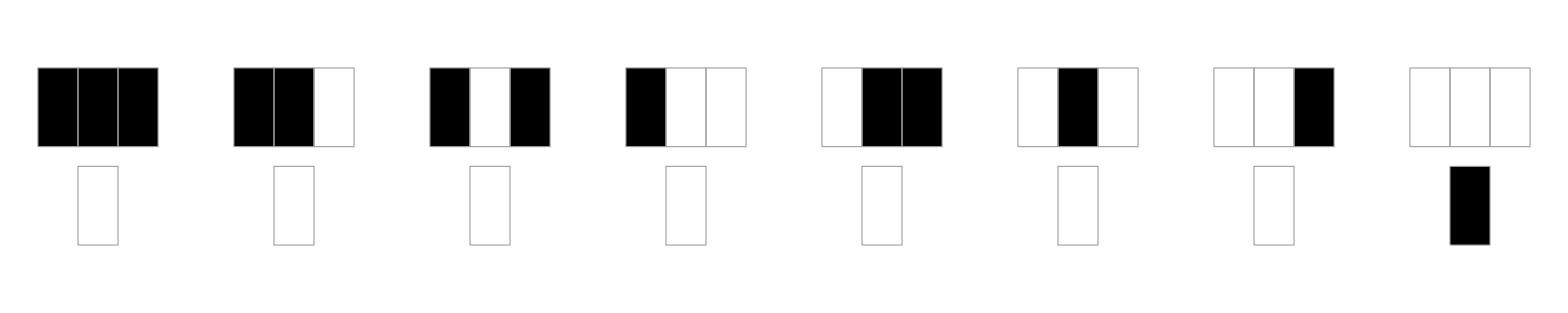
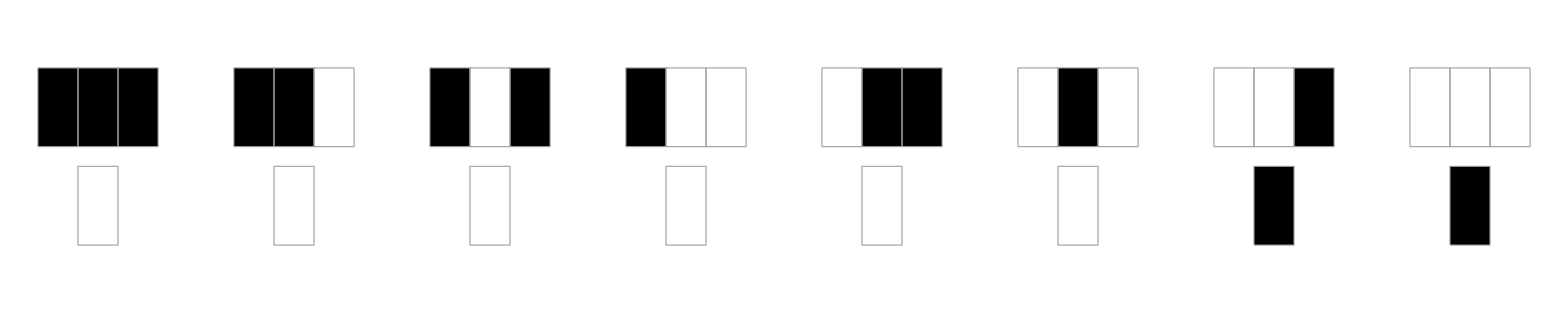
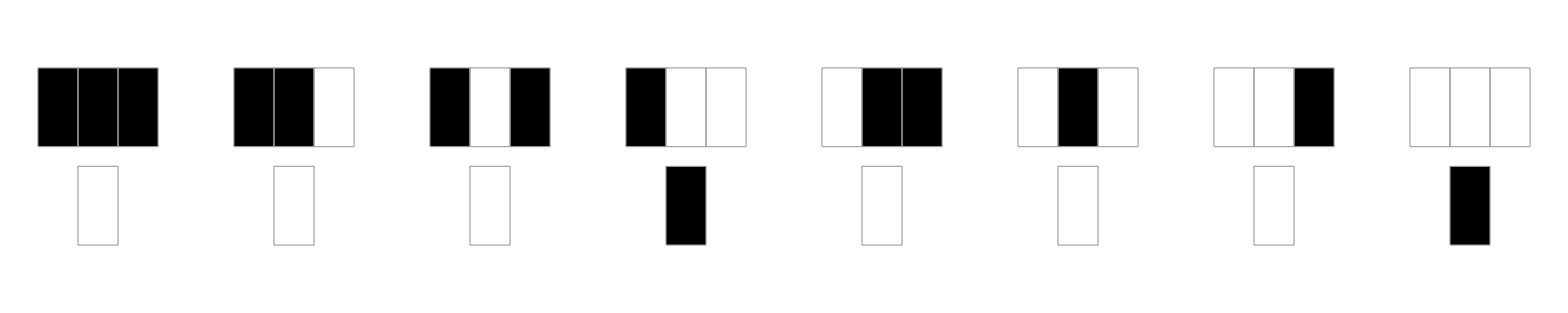
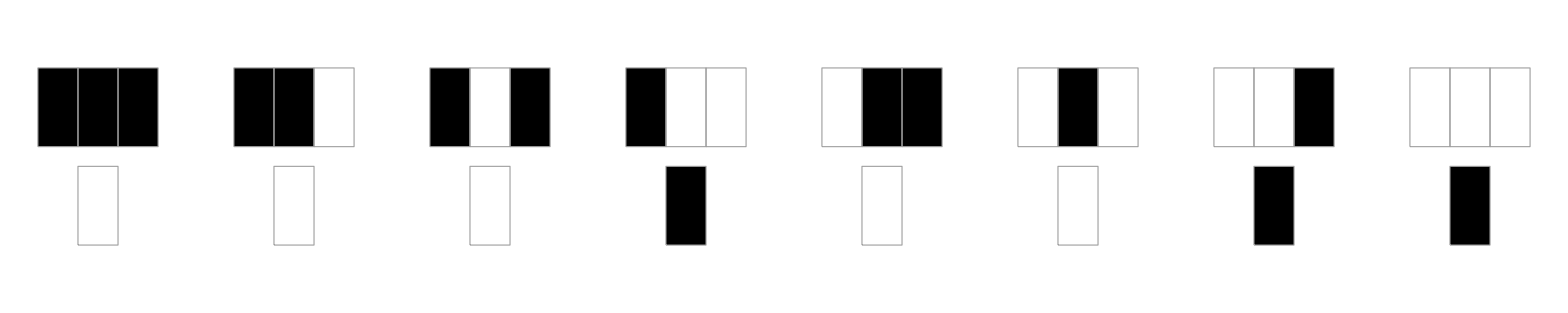
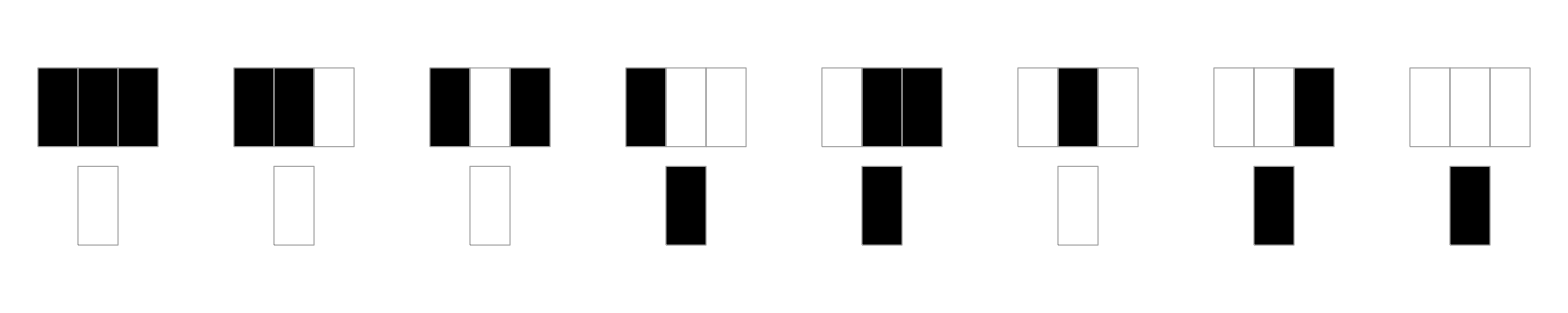
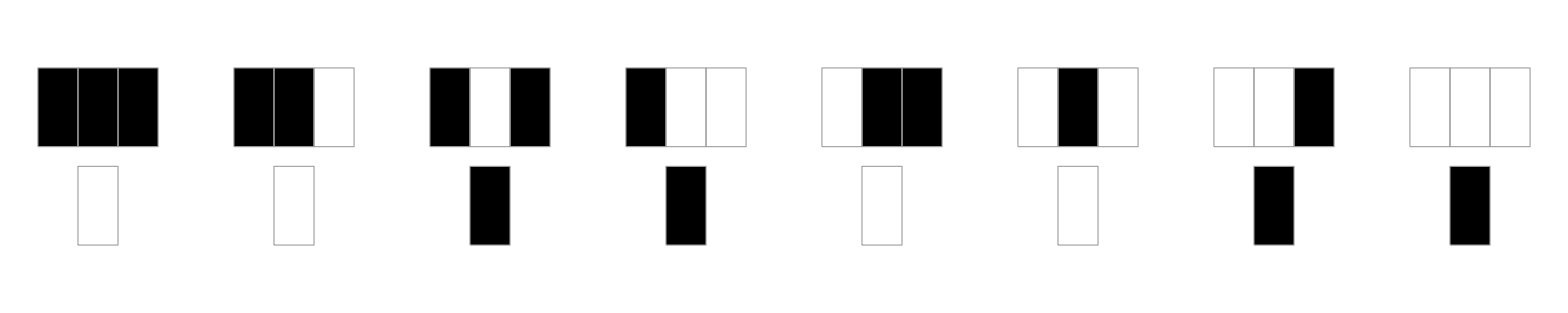
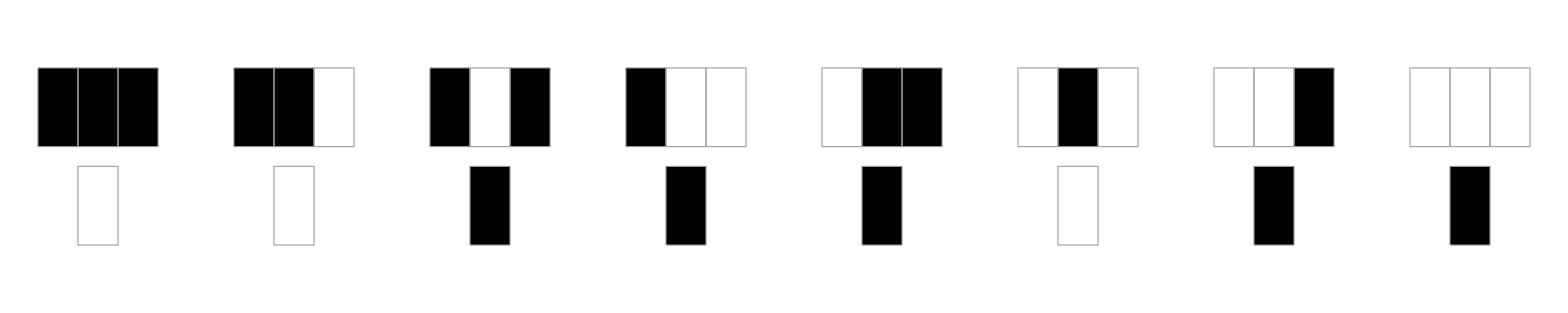
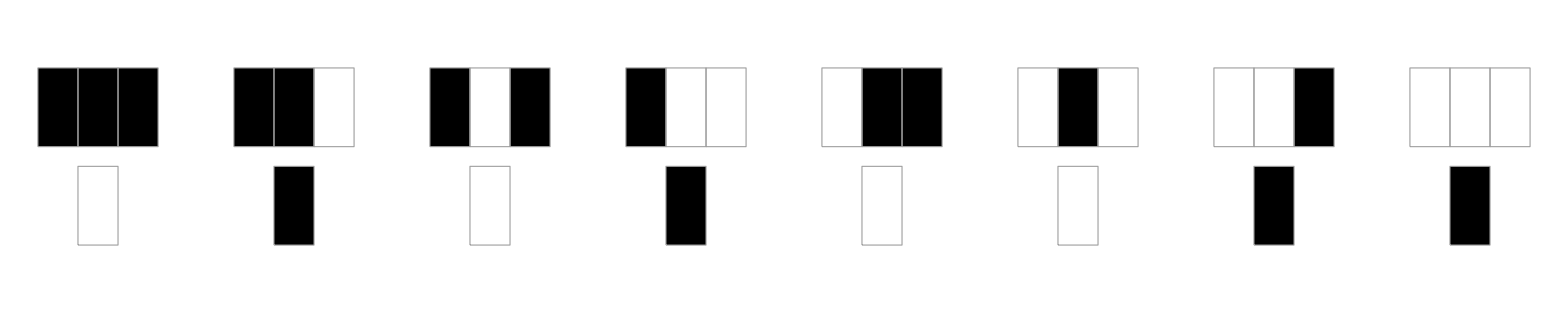
(1 | -Graphics-
3 | -Graphics-
17 | -Graphics-
19 | -Graphics-
27 | -Graphics-
51 | -Graphics-
59 | -Graphics-
83 | -Graphics-
91 | -Graphics-
115 | -Graphics-
123 | -Graphics-
139 | -Graphics-
201 | -Graphics-
209 | -Graphics-
255 | -Graphics-)

```mathematica
{#,RulePlot[CellularAutomaton[#]]}&/@{1,3,17,19,27,51,59,83,91,115,123,139,201,209,255}//MatrixForm
```

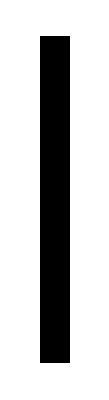
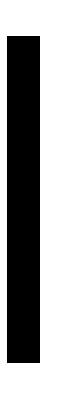
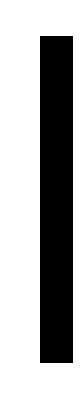
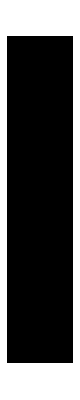
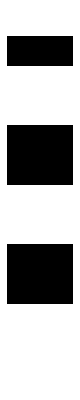
{{1,-Graphics-},{3,-Graphics-},{17,-Graphics-},{19,-Graphics-},{27,-Graphics-},{51,-Graphics-},{59,-Graphics-},{83,-Graphics-},{91,-Graphics-},{115,-Graphics-},{123,-Graphics-},{139,-Graphics-},{201,-Graphics-},{209,-Graphics-},{255,-Graphics-}}

```mathematica
{#,ArrayPlot[CellularAutomaton[{CA2CARev[#],2,1,2},{{{1},{1}},0},10]]}&/@{1,3,17,19,27,51,59,83,91,115,123,139,201,209,255}
```

### Representing the rules in algebraic form, with acyclic configurations of the form { { {1}, {1} }, 0 }

#### ECA 150, Mod[ p + q + r, 2 ]: reversible

```mathematica
Module[{tsteps={{-1,100}},auxCA},
Print@ArrayPlot[CellularAutomaton[
{If[#⟦1⟧==0,
Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧,2],
1-Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧,2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{{{1},{1}},0},tsteps]];
auxCA=CellularAutomaton[
{If[#⟦1⟧==0,
Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧,2],
1-Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧,2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{{{1},{1}},0},tsteps]⟦-2;;-1⟧;
Print@ArrayPlot[CellularAutomaton[
{If[#⟦1⟧==0,
Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧,2],
1-Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧,2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{Reverse[auxCA],0},tsteps]]]
```

-Graphics-

-Graphics-

#### ECA 214, Mod[ p + q + r + pq + pqr, 2 ]: reversible

```mathematica
Module[{tsteps={{-1,100}},auxCA},
Print@ArrayPlot[CellularAutomaton[
{If[#⟦1⟧==0,
Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧+#⟦2⟧#⟦3⟧+#⟦2⟧#⟦3⟧#⟦4⟧,2],
1-Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧+#⟦2⟧#⟦3⟧+#⟦2⟧#⟦3⟧#⟦4⟧,2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{{{1},{1}},0},tsteps]];
auxCA=CellularAutomaton[
{If[#⟦1⟧==0,
Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧+#⟦2⟧#⟦3⟧+#⟦2⟧#⟦3⟧#⟦4⟧,2],
1-Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧+#⟦2⟧#⟦3⟧+#⟦2⟧#⟦3⟧#⟦4⟧,2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{{{1},{1}},0},tsteps]⟦-2;;-1⟧;
Print@ArrayPlot[CellularAutomaton[
{If[#⟦1⟧==0,
Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧+#⟦2⟧#⟦3⟧+#⟦2⟧#⟦3⟧#⟦4⟧,2],
1-Mod[#⟦2⟧+#⟦3⟧+#⟦4⟧+#⟦2⟧#⟦3⟧+#⟦2⟧#⟦3⟧#⟦4⟧,2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{Reverse[auxCA],0},tsteps]]]
```

-Graphics-

-Graphics-

#### ECA 5, Mod[ (1 + p) (1 + r), 2 ]: non reversible

```mathematica
Module[{tsteps={{-1,100}},auxCA},
Print@ArrayPlot[CellularAutomaton[
{If[#⟦1⟧==0,
Mod[(1+#⟦2⟧)(1+#⟦4⟧),2],
1-Mod[(1+#⟦2⟧)(1+#⟦4⟧),2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{{{1},{1}},0},tsteps]];
auxCA=CellularAutomaton[
{If[#⟦1⟧==0,
Mod[(1+#⟦2⟧)(1+#⟦4⟧),2],
1-Mod[(1+#⟦2⟧)(1+#⟦4⟧),2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{{{1},{1}},0},tsteps]⟦-2;;-1⟧;
Print@ArrayPlot[CellularAutomaton[
{If[#⟦1⟧==0,
Mod[(1+#⟦2⟧)(1+#⟦4⟧),2],
1-Mod[(1+#⟦2⟧)(1+#⟦4⟧),2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{Reverse[auxCA],0},tsteps]]]
```

-Graphics-

-Graphics-

#### ECA 89, Mod[ 1 + q + r + pq, 2 ]: non reversible

```mathematica
Module[{tsteps={{-1,100}},auxCA},
Print@ArrayPlot[CellularAutomaton[
{If[#⟦1⟧==0,
Mod[1+#⟦3⟧+#⟦4⟧ + #⟦2⟧#⟦3⟧,2],
1-Mod[1+#⟦3⟧+#⟦4⟧ + #⟦2⟧#⟦3⟧,2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{{{1},{1}},0},tsteps]];
auxCA=CellularAutomaton[
{If[#⟦1⟧==0,
Mod[1+#⟦3⟧+#⟦4⟧ + #⟦2⟧#⟦3⟧,2],
1-Mod[1+#⟦3⟧+#⟦4⟧ + #⟦2⟧#⟦3⟧,2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{{{1},{1}},0},tsteps]⟦-2;;-1⟧;
Print@ArrayPlot[CellularAutomaton[
{If[#⟦1⟧==0,
Mod[1+#⟦3⟧+#⟦4⟧ + #⟦2⟧#⟦3⟧,2],
1-Mod[1+#⟦3⟧+#⟦4⟧ + #⟦2⟧#⟦3⟧,2]]&,
{},{{-1,0},{0,-1},{0,0},{0,1}},2},{Reverse[auxCA],0},tsteps]]]
```

-Graphics-

-Graphics-